```mathematica
bins[ z_, a_] := Product[ (z-k),{k,0,a-1}]/a!
L2[n_, k_ ]:= L2[n,k]=Sum[ L2[Floor[n/j],k-1],{j,2,n}];L2[n_, 1] := Sum[ Log[j],{j,2,n}];L2[n_, 0] := 1
L1[n_,z_]:=Sum[bins[z-1,a] L2[n,a+1],{a,0,Log[2,n]}]
L1a[n_,z_]:=Sum[bins[z,a] L2[n,a],{a,0,Log[2,n]}]
L1b[n_,z_]:=(Sum[bins[z,a] L2[n,a],{a,0,Log[2,n]}]-1)/z
```

```mathematica
N[L1a[100,1]]
```

363.739

```mathematica
N[L1[100,0]]
```

94.0453

```mathematica
Expand[N[(L1a[100.,z])]]
```

192.184 z+129.802 z^2+36.4475 z^3+5.0375 z^4+0.261138 z^5+0.00730208 z^6

```mathematica
(List@@NRoots[ (L1a[100,x]/x)==0,x][[All,2]])
```

{-12.9799-15.0426 ⅈ,-12.9799+15.0426 ⅈ,-3.68065,-3.06086-2.95722 ⅈ,-3.06086+2.95722 ⅈ}

```mathematica
Expand[N[L1[100.,z]]]
```

94.0453+169.15 z+81.6195 z^2+17.6846 z^3+1.19616 z^4+0.0438125 z^5

```mathematica
Roots[ L1[10,x]==0,x]
```

x==1/(2 Log[2])(-5 Log[2]-4 Log[3]-2 Log[4]-2 Log[5]-√((5 Log[2]+4 Log[3]+2 Log[4]+2 Log[5])^2-4 Log[2] (-4 Log[2]-2 Log[3]+2 Log[6]+2 Log[7]+2 Log[8]+2 Log[9]+2 Log[10])))||x==1/(2 Log[2])(-5 Log[2]-4 Log[3]-2 Log[4]-2 Log[5]+√((5 Log[2]+4 Log[3]+2 Log[4]+2 Log[5])^2-4 Log[2] (-4 Log[2]-2 Log[3]+2 Log[6]+2 Log[7]+2 Log[8]+2 Log[9]+2 Log[10])))

```mathematica
Expand[L1[10,z]]
```

-2 Log[2]+5/2 z Log[2]+1/2 z^2 Log[2]-Log[3]+2 z Log[3]+z Log[4]+z Log[5]+Log[6]+Log[7]+Log[8]+Log[9]+Log[10]

```mathematica
f1[z_] := 7.8320141805054675+6.925824802290074 z+0.34657359027997264 z^2
```

```mathematica
f1[1]
```

15.1044

```mathematica
f2[z_] := (z-(-18.780408851506877))(z-(-1.2032973411524708))(Log[2]/2)
```

```mathematica
f2[0]
```

7.83201

```mathematica
f1[0]
```

7.83201

```mathematica
Expand[ ( z-(-18.780408851506877))(z-(-1.2032973411524708))]
```

```mathematica
Expand[(22.59841603677455+19.983706192659348 z+z^2)*0.34657359027997264]
```

7.83201+6.92582 z+0.346574 z^2

```mathematica
.5 Log[2]
```

0.346574

```mathematica
N[Roots[ L1[10,x]==0,x]]
```

x==-18.7804||x==-1.2033

```mathematica
N[Roots[Expand[ DDa[10,x]]==0,x]]
```

x==-0.218507+3.55271×10^-15 ⅈ||x==-1.41809-3.55271×10^-15 ⅈ||x==-19.3634+1.66533×10^-16 ⅈ

```mathematica
K[n_]:=If[n==1,0,FullSimplify[MangoldtLambda[n]/Log[n]]]
P[n_,k_]:=P[n,k]=Sum[ K[j]P[Floor[n/j],k-1],{j,2,n}];P[n_,0]:=1
D2[n_,k_]:=D2[n,k]=Sum[D2[Floor[n/j],k-1],{j,2,n}];D2[n_,0]:=1
DD[n_,z_]:=Sum[FactorialPower[z,a]/a! D2[n,a],{a,0,Log[2,n]}]
P[n_,k_,s_]:=P[n,k,s]=Sum[ j^-s K[j]P[Floor[n/j],k-1,s],{j,2,n}];P[n_,0,s_]:=1
DDa[n_, z_] := Sum[ z^k/k! P[n,k],{k,0,Log[2,n]}]
DDa[n_, z_,s_] := Sum[ z^k/k! P[n,k,s],{k,0,Log[2,n]}]
DDa2[n_, z_] := Sum[ z^k/k! P[n,k]/z,{k,0,Log[2,n]}]
```

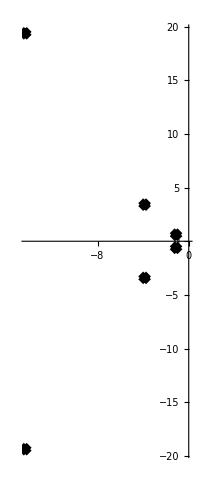

```mathematica
RootLocusPlot[1/Expand[L1[200,x]],{k,0,1},FeedbackType->None]
```

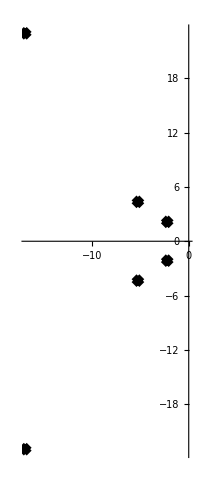

```mathematica
RootLocusPlot[1/Expand[L1a[200,x]/x],{k,0,1},FeedbackType->None]
```

```mathematica
(List@@NRoots[ (L1a[100,x]/x)==0,x][[All,2]])
```

{-12.9799-15.0426 ⅈ,-12.9799+15.0426 ⅈ,-3.68065,-3.06086-2.95722 ⅈ,-3.06086+2.95722 ⅈ}

```mathematica
Expand[N[L1a[100.,z]/z]]
```

192.184+129.802 z+36.4475 z^2+5.0375 z^3+0.261138 z^4+0.00730208 z^5

```mathematica
vv:={-12.979912222112542-15.042599906951901 ⅈ,-12.979912222112542+15.042599906951901 ⅈ,-3.6806513834840673,-3.060857811799053-2.957220916607718 ⅈ,-3.060857811799053+2.957220916607718 ⅈ}
```

```mathematica
[ 1+1/j,{j,vv}]
```

94.0453+0. ⅈ

```mathematica
Expand[N[(L1[100.,z+1])]]
```

363.739+390.447 z+142.289 z^2+22.9074 z^3+1.41522 z^4+0.0438125 z^5

```mathematica
(List@@NRoots[ (L1[100,x+1])==0,x][[All,2]])
```

{-11.6971-12.1994 ⅈ,-11.6971+12.1994 ⅈ,-3.53645-1.82621 ⅈ,-3.53645+1.82621 ⅈ,-1.83471}

```mathematica
v2 := {-11.697109591508216-12.199354854259528 ⅈ,-11.697109591508216+12.199354854259528 ⅈ,-3.5364503360079835-1.8262103341135596 ⅈ,-3.5364503360079835+1.8262103341135596 ⅈ,-1.8347063543903144}
```

```mathematica
N[Log[100!]]Product[ 1+1/j,{j,v2}]
```

94.0453-2.52395×10^-15 ⅈ

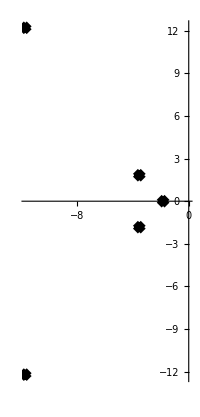

```mathematica
RootLocusPlot[1/Expand[L1[100,x+1]],{k,0,1},FeedbackType->None]
```

```mathematica
{-11.697109591508216-12.199354854259528 ⅈ,-11.697109591508216+12.199354854259528 ⅈ,-3.5364503360079835-1.8262103341135596 ⅈ,-3.5364503360079835+1.8262103341135596 ⅈ,-1.8347063543903144}
```

```mathematica
{-11.199685576035792-12.398224487807212 ⅈ,-11.199685576035792+12.398224487807212 ⅈ,-2.6719503346754907-1.8618449055430242 ⅈ,-2.6719503346754907+1.8618449055430242 ⅈ,-0.9338092178222006,-0.03720467504094745}
```

```mathematica
(List@@NRoots[ (L1a[100,x]/x)==0,x][[All,2]])
```

{-12.9799-15.0426 ⅈ,-12.9799+15.0426 ⅈ,-3.68065,-3.06086-2.95722 ⅈ,-3.06086+2.95722 ⅈ}

```mathematica
v3 := {-12.979912222112542-15.042599906951901 ⅈ,-12.979912222112542+15.042599906951901 ⅈ,-3.6806513834840673,-3.060857811799053-2.957220916607718 ⅈ,-3.060857811799053+2.957220916607718 ⅈ}
```

```mathematica
Log[100!] Product[ 1+2/(j-1),{j,v3}]
```

94.0453+0. ⅈ

```mathematica
(List@@NRoots[ (L1a[100,x])==0,x][[All,2]])
```

{-12.9799-15.0426 ⅈ,-12.9799+15.0426 ⅈ,-3.68065,-3.06086-2.95722 ⅈ,-3.06086+2.95722 ⅈ,0.}

```mathematica
(List@@NRoots[ (L1a[100,x]/x)==0,x][[All,2]])
```

{-12.9799-15.0426 ⅈ,-12.9799+15.0426 ⅈ,-3.68065,-3.06086-2.95722 ⅈ,-3.06086+2.95722 ⅈ}

```mathematica
(List@@NRoots[ (L1[100,x+1])==0,x][[All,2]])
```

{-11.6971-12.1994 ⅈ,-11.6971+12.1994 ⅈ,-3.53645-1.82621 ⅈ,-3.53645+1.82621 ⅈ,-1.83471}

```mathematica
N[Expand[L1a[100,z]]]
```

1.+192.184 z+129.802 z^2+36.4475 z^3+5.0375 z^4+0.261138 z^5+0.00730208 z^6

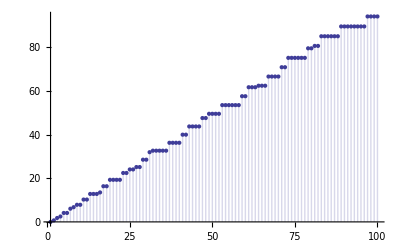

```mathematica
DiscretePlot[1-L1a[n,-1],{n,1,100}]
```

```mathematica
(List@@NRoots[ (L1a[100,x])==0,x][[All,2]])
```

{-12.9799-15.0426 ⅈ,-12.9799+15.0426 ⅈ,-3.66756,-3.06482-2.95324 ⅈ,-3.06482+2.95324 ⅈ,-0.00522175}

```mathematica
v4 := {-12.979886712505683-15.04256868566443 ⅈ,-12.979886712505683+15.04256868566443 ⅈ,-3.667560789512249,-3.0648177458685923-2.953236749181686 ⅈ,-3.0648177458685923+2.953236749181686 ⅈ,-0.005221745046451817}
```

```mathematica
Product[ 1-1/j,{j,v4}]-1
```

363.739+0. ⅈ

```mathematica
N[Log[100!]]
```

363.739

```mathematica
N[L1a[100,1]]-1
```

363.739

```mathematica
N[ Sum[ MangoldtLambda[ j ],{j,1,100}]]
```

94.0453

```mathematica
1-N[L1a[100,-1]]
```

94.0453

```mathematica
1-Product[ 1+1/j,{j,v4}]
```

94.0453+0. ⅈ

```mathematica
(1+1/List@@NRoots[ (L1a[100,x])==0,x][[All,2]])
```

{0.967119+0.038106 ⅈ,0.967119-0.038106 ⅈ,0.727339,0.830811+0.16303 ⅈ,0.830811-0.16303 ⅈ,-190.507}

```mathematica
Sum[ -1/j,{j,v4}]
```

192.184+0. ⅈ

```mathematica
(1+1/List@@NRoots[ (L1a[100,x])==0,x][[All,2]])
```

{0.967119+0.038106 ⅈ,0.967119-0.038106 ⅈ,0.727339,0.830811+0.16303 ⅈ,0.830811-0.16303 ⅈ,-190.507}